Setup of the Problem

```mathematica
(* We follow the notation and parameterization from Dunne Wang 2006 *)
(* phi is in expectation value units *)
```

```mathematica
SetDirectory[NotebookDirectory[]];
<<MaTeX`
SetOptions[MaTeX,"Preamble"->{"\\usepackage{color}"}];
sigmaTicks={0,{Pi/4,MaTeX["\\frac{\\pi}{4}",Magnification->1.2]},{Pi/2,MaTeX["\\frac{\\pi}{2}",Magnification->1.2]},{3Pi/4,MaTeX["\\frac{3\\pi}{4}",Magnification->1.2]},{Pi,MaTeX["\\pi",Magnification->1.2]}};
VV = beta*H^2 *vev^2(1/(beta* epsilon^2)- phi^2/2-b/3*(phi)^3+1/4*(phi)^4);
vPrime =D[VV,phi];
rules = {beta->45, b->25/100, epsilon->46/1000,H->1};
tol = 10^(-15);
chiMin=1/10000;
chiMax = Pi-chiMin;
```

```mathematica
phiMinR =phi/.Solve[vPrime==0,phi][[-1]]
phiMinL =phi/.Solve[vPrime==0,phi][[2]]
```

1/2 (b+√(4+b^2))

1/2 (b-√(4+b^2))

```mathematica
N[phiMinR/.rules,40]
```

1.132782218537318706545826653787971391392

```mathematica
{Limit[H0*Cot[H0 chi],H0->0],Limit[H0*Cot[H0 chi],H0->Pi/chi]}
```

{1/chi,Indeterminate}

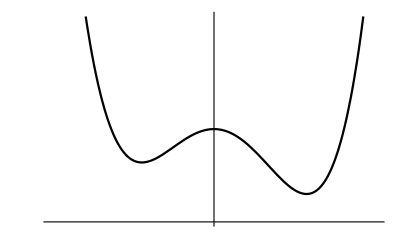

```mathematica
Plot[VV/(H^2*vev^2)/.rules,{phi,-2,2},PlotRange->{Automatic,{450,500}},PlotStyle->{Black},AxesLabel->{MaTeX["\\phi",Magnification->1.5],MaTeX["V(\\phi)",Magnification->1.5]},Ticks->{{{phiMinL/.rules,MaTeX["\\phi_-",Magnification->1.5]},{phiMinR/.rules,MaTeX["\\phi_+",Magnification->1.5]}}}]
```

Finding the bounce solution by digits

```mathematica
eqBounce = h''[chi]+ 3 Cot[chi] h'[chi]==vPrime/(H^2*vev^2)/.Join[{phi->h[chi]},rules];
findStart[initPos_,digit_]:= Module[{step=10^(-digit),bounce,iterCounter,newStartPos},
newStartPos=initPos;
ClearAll[bounce];
bounce=h/.NDSolve[{eqBounce,h[chiMin]==initPos,h'[chiMin]==0},h,{chi,chiMin,chiMax},WorkingPrecision->40,MaxSteps->90000, Method->{"StiffnessSwitching",Method->{Automatic,Automatic}},AccuracyGoal->10][[1]];
Print[Plot[{bounce[chi],phiMinL/.rules},{chi,chiMin,chiMax},PlotRange->{{0,Pi},{phiMinL/.rules,phiMinR/.rules}},PlotRangePadding->Scaled[.1],PlotStyle->{Line,Dashed}]];
(*Print[ bounce'[bounce["Domain"][[-1,-1]]-tol]];*)
iterCounter =0;
While[( bounce'[bounce["Domain"][[-1,-1]]-tol]>0) && iterCounter<=10&& newStartPos<1.132782218537318706545826653787971391391799538201071673492`40.,
newStartPos=newStartPos+step;
Print[N[newStartPos,25]];
Print[ bounce'[bounce["Domain"][[-1,-1]]]];
ClearAll[bounce];
bounce=h/.NDSolve[{eqBounce,h[chiMin]==newStartPos,h'[chiMin]==0},h,{chi,chiMin,chiMax},WorkingPrecision->40,MaxSteps->90000, Method->{"StiffnessSwitching",Method->{Automatic,Automatic}},AccuracyGoal->10][[1]];
If[Mod[iterCounter,10]==0,Print[iterCounter];Print[N[newStartPos,24]],{}];
iterCounter= iterCounter+1;
];
If[(iterCounter>0),
bounce=h/.NDSolve[{eqBounce,h[chiMin]==newStartPos-step,h'[chiMin]==0},h,{chi,chiMin,chiMax},WorkingPrecision->40,MaxSteps->90000, Method->{"StiffnessSwitching",Method->{Automatic,Automatic}},AccuracyGoal->10,InterpolationOrder->All][[1]];Print[N[newStartPos-step,30]];];
Print[bounce["Domain"][[-1,-1]]];
Return[bounce];];
```

```mathematica
(* STARTING POINT for old parameters 11322304816551528889700*10^(-22) *)
```

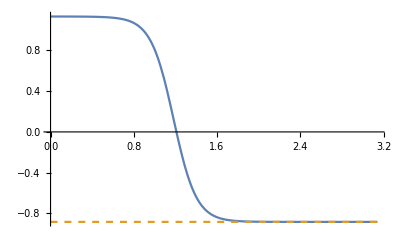

1.1322304816551528889701

1.046081262371190380644683146466445

0

1.1322304816551528889701

1.1322304816551528889702

1.029041213475222212838854030112084

1.1322304816551528889703

1.01200116403878807849344629445594

1.1322304816551528889704

0.9949611140322206017937014004178479

1.1322304816551528889705

0.9779210634237425469978947149156279

1.1322304816551528889706

0.9608810121792702956140879615955105

1.1322304816551528889707

0.9438409602621946011491729451210352

1.1322304816551528889708

0.9268009076331354764605951743049463

1.1322304816551528889709

0.9097608542496675604199935115579902

1.132230481655152888971

0.8927208000660117080372732337903976

1.1322304816551528889711

0.8756807450326878316214481923690806

10

1.1322304816551528889711

1.132230481655152888971

3.141492653589793238462643383279502884197

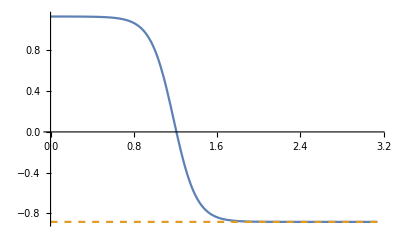

```mathematica
bounce=findStart[11322304816551528889700*10^(-22),22];
Plot[{bounce[chi],phiMinL/.rules},{chi,chiMin,chiMax},PlotRange->{{0,Pi},{phiMinL/.rules,phiMinR/.rules}},PlotRangePadding->Scaled[.1],PlotStyle->{Line,Dashed}]
```

```mathematica
bounce[chiMin]
```

1.132230481655152888971

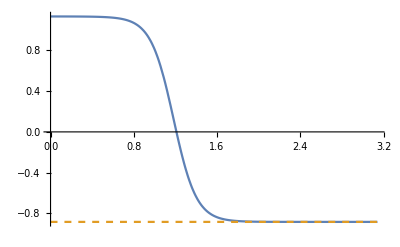

```mathematica
Plot[{bounce[chi],phiMinL/.rules},{chi,chiMin,chiMax},PlotRange->{{0,Pi},Automatic},PlotRangePadding->Scaled[.1],PlotStyle->{Line,Dashed}]
```

```mathematica
FindRoot[D[bounce[x],x],{x,2}]
```

{x→3.12933}

```mathematica
ClearAll[bounceExtended]
```

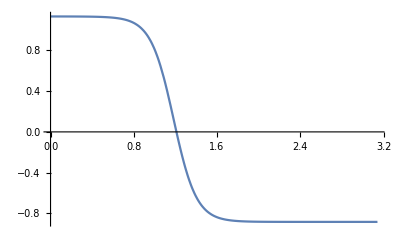

```mathematica
bounceExtended[chi_]=Piecewise[{{bounce[chiMin],chi<chiMin},{bounce[chi],chiMin≤chi<chiMax},{bounce[chiMax],chi≥chiMax}}];
Plot[bounceExtended[chi],{chi,0,Pi}]
Put[bounceExtended[chi],"bounceJuanNewParameters.wdx"];
```

{π,-0.882778968128473}

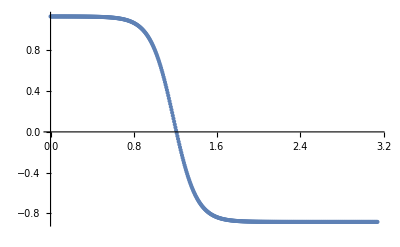

```mathematica
bounceExtendedTable=Table[{chi,N[bounceExtended[chi],15]},{chi,0,Pi,Pi/500}];
bounceExtendedTable//Last
ListPlot[bounceExtendedTable]
```

Defining a module for precision interpolation

```mathematica
splineInterp[data_,order_,x_]:=Module[{m=order,xa,ya},
n=Length[data];
{xa,ya}=Transpose[data];
knots=Join[ConstantArray[xa[[1]],m+1],If[m+2≤n,MovingAverage[ArrayPad[xa,-1],m],{}],ConstantArray[xa[[-1]],m+1]];
cp=LinearSolve[Outer[BSplineBasis[{m,knots},#2,#1]&,xa,Range[0,Length[data]-1]],ya];
cp.Table[BSplineBasis[{m,knots},j-1,x],{j,n}]];
```

```mathematica
ClearAll[bounceExtendedInterp]
```

```mathematica
bounceExtendedRaw[chi_]= splineInterp[bounceExtendedTable,2,chi];
```

```mathematica
bounceExtendedInterp[chi_]:=bounceExtendedRaw[SetPrecision[chi,15]];
```

```mathematica
bounceExtendedInterp[1.2646468463514684532]//AbsoluteTiming
```

{0.483895,-0.235752392333}

```mathematica
bounceExtendedInterpAuto = Interpolation[bounceExtendedTable,Method->"Spline",InterpolationOrder->1];
bounceExtendedInterpAuto2 = Interpolation[bounceExtendedTable,Method->"Hermite",InterpolationOrder->1];
```

```mathematica
bounceExtendedInterp[0.5]
```

1.127002791031

```mathematica
bounceExtendedInterp[1.31684784653135498687]//AbsoluteTiming
```

{0.493718,-0.424781376495}

```mathematica
bounceExtendedInterp[0.531354684321543135135]
```

1.1254696865

```mathematica
plotBounceTable=Table[{chi,bounceExtendedInterp[chi]-bounceExtendedInterpAuto2[chi]},{chi,0,Pi,Pi/100}]//AbsoluteTiming
```

{49.0872,{{0,0.},{π/100,0.},{π/50,0.},{(3 π)/100,0.},{π/25,0.},{π/20,0.},{(3 π)/50,0.},{(7 π)/100,0.},{(2 π)/25,0.},{(9 π)/100,0.},{π/10,0.},{(11 π)/100,0.},{(3 π)/25,0.},{(13 π)/100,0.},{(7 π)/50,0.},{(3 π)/20,0.},{(4 π)/25,0.},{(17 π)/100,0.},{(9 π)/50,0.},{(19 π)/100,0.},{π/5,0.},{(21 π)/100,0.},{(11 π)/50,0.},{(23 π)/100,0.},{(6 π)/25,0.},{π/4,0.},{(13 π)/50,0.},{(27 π)/100,0.},{(7 π)/25,0.},{(29 π)/100,0.},{(3 π)/10,0.},{(31 π)/100,0.},{(8 π)/25,0.},{(33 π)/100,0.},{(17 π)/50,0.},{(7 π)/20,0.},{(9 π)/25,0.},{(37 π)/100,0.},{(19 π)/50,0.},{(39 π)/100,0.},{(2 π)/5,0.},{(41 π)/100,0.},{(21 π)/50,0.},{(43 π)/100,0.},{(11 π)/25,0.},{(9 π)/20,0.},{(23 π)/50,0.},{(47 π)/100,0.},{(12 π)/25,0.},{(49 π)/100,0.},{π/2,0.},{(51 π)/100,0.},{(13 π)/25,0.},{(53 π)/100,0.},{(27 π)/50,0.},{(11 π)/20,0.},{(14 π)/25,0.},{(57 π)/100,0.},{(29 π)/50,0.},{(59 π)/100,0.},{(3 π)/5,0.},{(61 π)/100,0.},{(31 π)/50,0.},{(63 π)/100,0.},{(16 π)/25,0.},{(13 π)/20,0.},{(33 π)/50,0.},{(67 π)/100,0.},{(17 π)/25,0.},{(69 π)/100,0.},{(7 π)/10,0.},{(71 π)/100,0.},{(18 π)/25,0.},{(73 π)/100,0.},{(37 π)/50,0.},{(3 π)/4,0.},{(19 π)/25,0.},{(77 π)/100,0.},{(39 π)/50,0.},{(79 π)/100,0.},{(4 π)/5,0.},{(81 π)/100,0.},{(41 π)/50,0.},{(83 π)/100,0.},{(21 π)/25,0.},{(17 π)/20,0.},{(43 π)/50,0.},{(87 π)/100,0.},{(22 π)/25,0.},{(89 π)/100,0.},{(9 π)/10,0.},{(91 π)/100,0.},{(23 π)/25,0.},{(93 π)/100,0.},{(47 π)/50,0.},{(19 π)/20,0.},{(24 π)/25,0.},{(97 π)/100,0.},{(49 π)/50,0.},{(99 π)/100,0.},{π,0.}}}

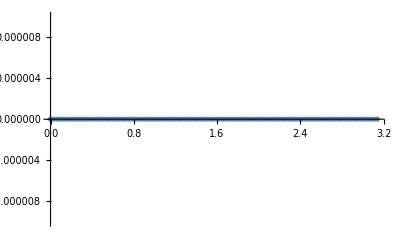

```mathematica
ListPlot[plotBounceTable[[2]],PlotRange->{{0,Pi},{-10^(-5),10^(-5)}}]
```

```mathematica
testD[chi_]=D[bounceExtendedInterp[x],x]/.{x->chi};
```

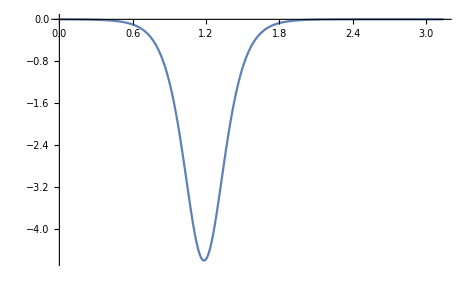
{403.241,-Graphics-}

```mathematica
Plot[Evaluate[testD[chi]],{chi,0,Pi},PlotRange->{{0,Pi},Full}]//AbsoluteTiming
```

```mathematica
Put[bounceExtendedInterp[chi],"bounceJuanHighPrec.wdx"];
```

Loading the saved bounce

```mathematica
ClearAll[bounceLoad]
bounceLoad[chi_]=Get["bounceExtended.wdx"];
```

```mathematica
B0 = NIntegrate[Sin[chi]^3*(1/2*(D[phi,chi])^2+VV/vev^2)/.Join[rules,{phi->bounceLoad[chi]}],{chi,chiMin,chiMax}]
```

619.546

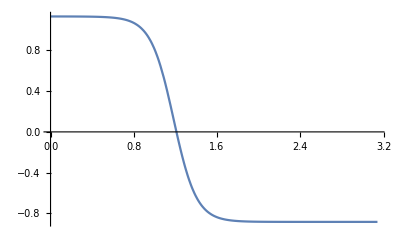

```mathematica
Plot[bounceLoad[chi],{chi,tol,Pi}]
```

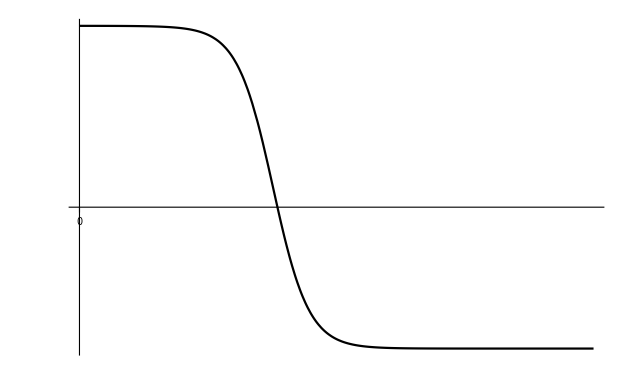

```mathematica
Plot[bounceLoad[chi],{chi,tol,Pi},PlotStyle->{Line,Black},PlotRange->{Full,Full},PlotRangePadding->Scaled[.05],Ticks->{sigmaTicks,{{phiMinL/.rules,MaTeX["\\phi_-",Magnification->1.2]},{phiMinR/.rules,MaTeX["\\phi_+",Magnification->1.2]}}},AxesLabel->{MaTeX["\\sigma \\quad \\bigg[\\frac{1}{H}\\bigg]",Magnification->1.2],None}]
```

Finding Green’s Function for the scalar

```mathematica
ClearAll[m2ϕEffInterp]
numpoints=200;
MyHeaviside[x_]=Piecewise[{{0,x<0},{1/2,x==0},{1,x>0}}];
chiMin=0+1/100000;
chiMax=Pi-chiMin;
m2ϕEff[bounce_,chi_]:=FullSimplify[(D[VV,{phi,2}]/vev^2)/H^2/.Join[rules,{phi->bounceLoad[chi]}]];
m2ϕEff[bounceLoad,chi];
m2ϕEffInterp := Interpolation[Table[{chi,m2ϕEff[bounceLoad,chi]},{chi,chiMin,Pi,(Pi-chiMin)/400}],Method->"Hermite",InterpolationOrder->1];
```

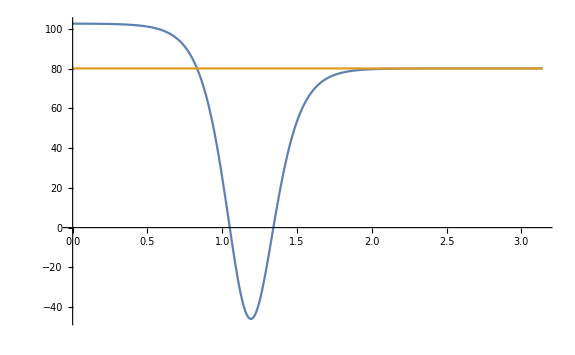

```mathematica
Plot[{Evaluate[(m2ϕEffInterp)[chi]],(m2ϕEffInterp)[Pi]},{chi,chiMin,chiMax},PlotRange->{Automatic,Full}]
```

```mathematica
Op[f_,ell_,chi_]:=(-3Cot[chi] D[f,chi]-D[D[f,chi],chi])+Sin[chi]^(-2)ell(ell+2)f+ m2ϕEffInterp[chi]f;
eq1[ell_,chi_]= Op[G[chi],ell,chi];
sol[ell_,pm_,equation_]:=If[pm==-1,NDSolve[{equation[ell,chi]==0,G[chiMin]==0,G'[chiMin]==1},G,{chi,chiMin,chiMax},WorkingPrecision->20(* 36 *),PrecisionGoal->10(* 12 *),MaxSteps->150000,InterpolationOrder->All,MaxStepSize->2*(chiMax-chiMin)/(2numpoints)],
NDSolve[{equation[ell,chi]==0,G[chiMax]==0,G'[chiMax]==-1},G,{chi,chiMin,chiMax},WorkingPrecision->20 (* 36 *),PrecisionGoal->10 (* 12 *),MaxSteps->150000,InterpolationOrder->All,MaxStepSize->2*(chiMax-chiMin)/(2numpoints)]];
f1less[eq_,ell_,chi_]:=G[chi]/.sol[ell,-1,eq][[1]];
f1great[eq_,ell_,chi_]:=G[chi]/.sol[ell,1,eq][[1]];
wronsk[eq_,ell_,chi_]:=-f1less[eq,ell,chi]*D[f1great[eq,ell,chi],chi] +f1great[eq,ell,chi]*D[f1less[eq,ell,chi],chi];
green[eq_,ell_,chi_,chiP_]:=(MyHeaviside[chiP-chi]*f1less[eq,ell,chi]*f1great[eq,ell,chiP]+MyHeaviside[chi-chiP]*f1great[eq,ell,chi]*f1less[eq,ell,chiP])*(H^(3) )/(wronsk[eq,ell,chiP])/.rules;
```

```mathematica
ClearAll[Op2,eq2];
Op2[f_,ell_,chi_]:=(-3Cot[chi] D[f,chi]-D[D[f,chi],chi])+Sin[chi]^(-2)ell(ell+2)f+ m2ϕEffInterp[Pi]f;
eq2[ell_,chi_]= Op2[G[chi],ell,chi];
```

```mathematica
test0[chi_,chiP_]=green[eq1,5,chi,chiP];
test1[chi_,chiP_]=green[eq2,5,chi,chiP];
Beep[];
```

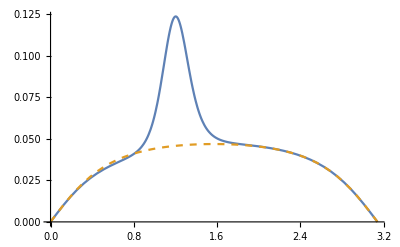

```mathematica
Plot[{test0[chi,chi],test1[chi,chi]},{chi,chiMin,chiMax},PlotStyle->{Line,Dashed},PlotRange->{Full,Full}]
```

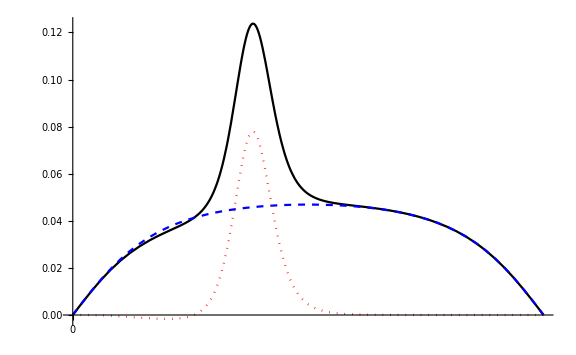

```mathematica
Plot[{test0[chi,chi],test1[chi,chi],test0[chi,chi]-test1[chi,chi](*,test0[chi,chi]/test1[chi,chi] *)},{chi,chiMin,chiMax},PlotStyle->{{Line,Black},{Dashed,Blue},{Dotted,Red},{Dashed,Blue},{Line,Blue}},PlotRange->{{chiMin,chiMax},Automatic},PlotLegends->Placed[{MaTeX["\\text{Solution over }\\phi_b",Magnification->1.2],MaTeX["\\text{Solution over }\\phi_{\\rm fv}",Magnification->1.2],MaTeX["\\text{Difference}",Magnification->1.2]},Above],ImageSize->Large,Ticks->{sigmaTicks,Automatic},AxesLabel->{MaTeX["\\sigma\\quad \\bigg[\\frac{1}{H}\\bigg]",Magnification->1.2],MaTeX["G_5(\\sigma,\\sigma)",Magnification->1.2]},LabelStyle->Directive[FontFamily->"Times",15,Black]]
```

```mathematica
wronsk1[chi_,flessTemp_ ,fgreatTemp_]:=-flessTemp[chi]*D[fgreatTemp[up],up] +fgreatTemp[chi]*D[flessTemp[up],up]/.{up->chi};
greenScalar[eq_,ell_,chi_,chiP_]:=Module[{f1lessEval,f1greatEval,wronskEval},
f1lessEval[pt_] = f1less[eq,ell,chi]/.{chi->pt};
f1greatEval[pt_] = f1great[eq,ell,chi]/.{chi->pt};
wronskEval[pt_] =wronsk1[chi,f1lessEval,f1greatEval]/.{chi->pt};
Return[(MyHeaviside[chiP-chi]*f1lessEval[chi]*f1greatEval[chiP]+MyHeaviside[chi-chiP]*f1greatEval[chi]*f1lessEval[chiP])*(H^(3))/(wronskEval[chiP])/.rules]];
```

{22.2042,Null}

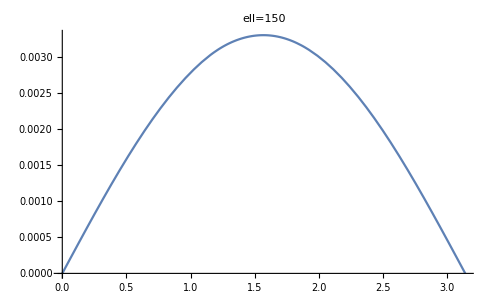

```mathematica
ellTest=150;
fun1[chi_,chiP_]=greenScalar[eq1,ellTest,chi,chiP];//AbsoluteTiming
Plot[fun1[chi,chi],{chi,chiMin,chiMax},PlotLabel->StringJoin["ell=",ToString[ellTest]]]
```

Checking quality of the solution

```mathematica
chiPTest=Pi/2;
ellTest=5;
test0[chi_,chiP_]=greenScalar[eq1,ellTest,chi,chiP];//AbsoluteTiming
test1[chi_,chiP_]=greenScalar[eq2,ellTest,chi,chiP];//AbsoluteTiming
```

{12.3756,Null}

{0.624917,Null}

```mathematica
NIntegrate[Op[test0[chi,chi],ellTest,chi],{chi,chiMin,chiMax}]
```

NIntegrate[Op[test0[chi,chi],ellTest,chi],{chi,chiMin,chiMax}]

70.9102

```mathematica
NIntegrate[Op[test1[chi,chi],ellTest,chi],{chi,chiMin,chiMax}]
```

NIntegrate[Op[test1[chi,chi],ellTest,chi],{chi,chiMin,chiMax}]

70.4988

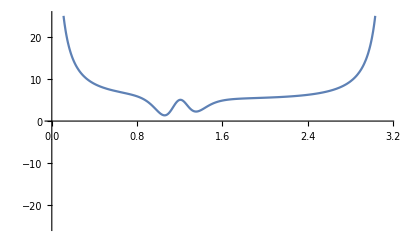

```mathematica
Plot[Op[test0[chi,chi],ellTest,chi]//Evaluate,{chi,chiMin,chiMax},PlotRange->{Automatic,{-25,25}}]
```

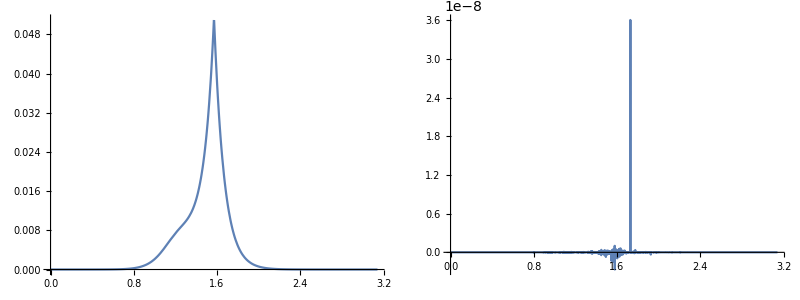

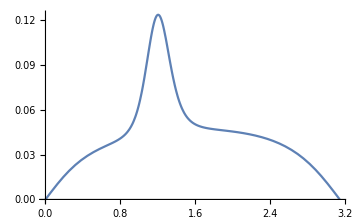
-Graphics- | -Graphics3D-

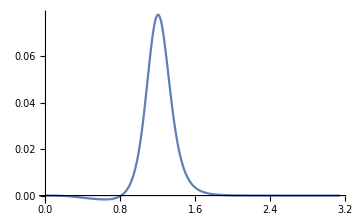
-Graphics- | -Graphics3D-

```mathematica
Grid[{{Plot[test0[chi,chiPTest],{chi,chiMin,chiMax},PlotRange->{Automatic,Full},ImageSize->Medium],
Plot[Evaluate[Op[test0[chi,chiPTest],ellTest,chi]],{chi,chiMin,chiMax},PlotRange->{Automatic,Full},ImageSize->Medium]}}]
Grid[{{Plot[test0[chi,chi],{chi,chiMin,chiMax},PlotRange->{Automatic,Automatic},ImageSize->Medium],Plot3D[Evaluate[test0[chi,chiP]],{chiP,chiMin,chiMax},{chi,chiMin,chiMax},PlotRange->{{chiMin,Pi},{chiMin,Pi},Full},PlotPoints->50,ImageSize->Medium]}}]
Grid[{{Plot[{test0[chi,chi]-test1[chi,chi]},{chi,chiMin,chiMax},PlotRange->{Automatic,Full},ImageSize->Medium],Plot3D[Evaluate[test0[chi,chiP]-test1[chi,chiP]],{chiP,chiMin,chiMax},{chi,chiMin,chiMax},PlotRange->{{0,Pi},{0,Pi},Full},PlotPoints->50,ImageSize->Medium]}}]
```

Scanning over Ell to reconstruct full Green’s function

```mathematica
reconstructed={};
For[ell=151,ell<201,ell++,
currentGreen[chi_,chiP_] = greenScalar[eq1,ell,chi,chiP];
reconstructed=Join[reconstructed,Table[{N[chiVal,15],ell,N[currentGreen[chiVal,chiVal],15]},{chiVal,chiMin,chiMax,(chiMax-chiMin)/500}]];
];//AbsoluteTiming
Export["tableGreenEll151-201NoSine.csv",reconstructed];
ClearAll[ell];
Beep[]
```

{784.801,Null}

```mathematica
ClearAll[reconstructed,reconstructed2point]
```

```mathematica
500*500
```

250000

```mathematica
UnsetShared[reconstructed2point]
```

{}

```mathematica
ClearAll[ell,reconstructed2point];
absolutePath=NotebookDirectory[];
ParallelDo[
Module[{ellTemp=ell,twoPtsList={}},
currentGreen[chi_,chiP_] = greenScalar[eq1,ellTemp,chi,chiP];
twoPtsList=Table[{N[chiVal,10],N[chiValP,10],N[ellTemp],N[currentGreen[chiVal,chiValP],10]},{chiVal,chiMin,chiMax,(chiMax-chiMin)/500},{chiValP,chiMin,chiMax,(chiMax-chiMin)/500}];
tempFileName=StringJoin[absolutePath,"twoPointGreenRaw\\green2Point",ToString[ellTemp],".csv"];
Export[tempFileName,twoPtsList,"CSV","TextDelimiters"->""]]
,{ell,0,100},Method->"CoarsestGrained"];//AbsoluteTiming

ClearAll[ell];
Beep[]
```

{2676.35,Null}

```mathematica
reconstructedFalseVacuum={};
For[ell=0,ell<101,ell++,
currentGreen[chi_,chiP_] = greenScalar[eq2,ell,chi,chiP];
reconstructedFalseVacuum=Join[reconstructedFalseVacuum,Chop[Table[{N[chiVal,15],ell,N[currentGreen[chiVal,chiVal],15]},{chiVal,chiMin,chiMax,(chiMax-chiMin)/500}],10^(-15)]];
]//AbsoluteTiming
Export["tableGreenFVEll100NoSine.csv",reconstructedFalseVacuum];
ClearAll[ell];
Beep[]
```

{625.771,Null}

Studying the results

```mathematica
reconstructed =Import["tableGreenEll100NoSine.csv"];
reconstructedFalseVacuum = Import["tableGreenFVEll100NoSine.csv"];
```

```mathematica
Grid[{{ListPlot3D[reconstructed,PlotRange->{Automatic,Automatic,{-1,1}},AxesLabel->{"chi","ell","Green"}],ListPlot3D[reconstructedFalseVacuum,PlotRange->{Automatic,Automatic,{-1,1}},AxesLabel->{"chi","ell","Green"}]}}]
```

-Graphics3D- | -Graphics3D-

```mathematica
tol=1/100000;
```

```mathematica
gradient= Chop[Table[{reconstructed[[i]][[1]],reconstructed[[i]][[2]],reconstructed[[i]][[3]]-reconstructedFalseVacuum[[i]][[3]]},{i,1,Length[reconstructed]}],10^(-20)]
```

{{0.00001,0,0},{0.00629315,0,-3.78142×10^-6},{0.0125763,0,-0.0000225807},{0.0188594,0,-0.0000615527},{0.0251426,0,-0.000122102},{0.0314257,0,-0.000203791},{0.0377089,0,-0.000305176},{0.043992,0,-0.00042427},50585,{3.0976,100,-6.91×10^-15},{3.10388,100,-4.38801×10^-15},{3.11017,100,-2.55799×10^-15},{3.11645,100,-1.31701×10^-15},{3.12273,100,-5.58012×10^-16},{3.12902,100,-1.65896×10^-16},{3.1353,100,-1.67984×10^-17},{3.14158,100,0}}
 |  |  |  |

```mathematica
gradient[[501]]
```

{3.14158,0,0}

```mathematica
gradientSorted= SortBy[Table[{reconstructed[[i]][[1]],reconstructed[[i]][[2]],reconstructed[[i]][[3]]},{i,1,Length[reconstructed],1}],#[[1]]&];
gradientSortedFV= SortBy[Table[{reconstructed[[i]][[1]],reconstructed[[i]][[2]],reconstructedFalseVacuum[[i]][[3]]},{i,1,Length[reconstructed],1}],#[[1]]&];
```

```mathematica
ListPlot3D[gradient,PlotRange->{Full,Full,{-1,1}}]
```

-Graphics3D-

```mathematica
(* Excluding negative and zero modes, the log identities should work *)
```

```mathematica
gradientRatioSum =Table[ {gradientSorted[[j,1]],Log[Check[Sum[gradientSorted[[i,3]](i-j+1)^2,{i,j+2,100+j}]/Sum[gradientSortedFV[[i,3]]*(i-j+1)^2,{i,j+2,100+j}],1]]},{j,1,Length[gradientSorted],101}];//Quiet
```

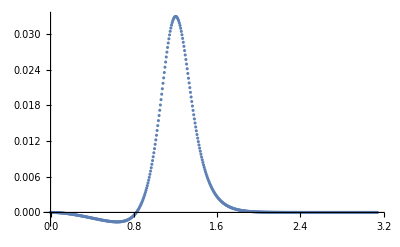

```mathematica
ListPlot[gradientRatioSum,PlotRange->Full]
```

```mathematica
gradientRatioSumInterp = Interpolation[gradientRatioSum,InterpolationOrder->1];
```

```mathematica
gradientRatioSumInterp[1.5]
```

0.00624953

```mathematica
NIntegrate[2Pi^2gradientRatioSumInterp[chi],{chi,chiMin,chiMax}]
```

0.22624

```mathematica
gradient[[0+1]]
```

{0.00001,0,0}

```mathematica
gg[ell_,chi_]=Interpolation[gradient,InterpolationOrder->1][chi,ell];
```

```mathematica
ggIntegrated[ell_]:= NIntegrate[gg[ell,chi],{chi,chiMin,chiMax},WorkingPrecision->10];
integrandNoZeroModes = Table[{ell,-(ell+1)^2ggIntegrated[ell]},{ell,2,100}];
```

```mathematica
Grid[{{ListPlot3D[gradient,PlotRange->{{chiMin,chiMax},{0,20},Full}],Plot3D[Log[(ell+1)^2gg[ell,chi]],{chi,tol,Pi-tol},{ell,0,10},PlotRange->{{0,Pi},Automatic,Full},PlotPoints->50]}}]
```

-Graphics3D- | -Graphics3D-

Estimate of the determinant assuming continuous sum over ell plus deformation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 6998.3401466553884264128449319060624374797896640095947709835692341 and 1.8446119729886913402343663475903022949211822099841277467711057126 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 7260.4683868487282200617890233929510787722051118926851761493265438 and 2.3416847612249004167191387726388605775160030794922740040580759386 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 7517.3522515890505200592430729811075000957331420496899992433899814 and 2.7485150730374796715497810459200840292909764503875167081531472438 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

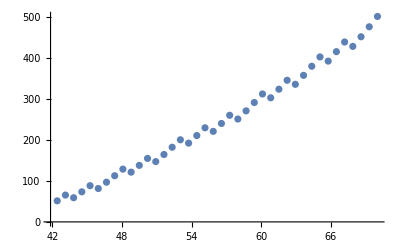

```mathematica
tableCutOff= {};
For[ellMax=60,ellMax<100,ellMax++,
detBare=-(1/2)(1/(2Pi^2))NIntegrate[k^2gg[Sqrt[k^2+s],chi],{k,1,ellMax/Sqrt[2]},{chi,tol,Pi-tol},{s,0,ellMax^2/2},WorkingPrecision->15];
ctIntegrated=(1/2)(1/(2Pi^2))Sum[(ell+1)^2*(alphaCT/(ell+1)+gammaCT/(ell+1)^3),{ell,2,ellMax/Sqrt[2],1}];
AppendTo[tableCutOff,{ellMax/Sqrt[2],detBare-ctIntegrated}];]
ListPlot[tableCutOff]
```

```mathematica
alphaCT = 1/2*NIntegrate[Sin[chi]*(m2ϕEffInterp[chi]-m2ϕEffInterp[Pi-tol]),{chi,chiMin,chiMax}]
```

-20.4577

```mathematica
gammaCT= NIntegrate[Sin[chi]*(m2ϕEffInterp[chi]-m2ϕEffInterp[Pi-tol])*((m2ϕEffInterp[chi]-m2ϕEffInterp[Pi-tol])*Sin[chi]^2-2(Cos[chi]^2+1)),{chi,chiMin,chiMax}]
```

3599.6

```mathematica
detRenorm = detBare-ctIntegrated
```

276.438

Attempt to scan s and ell to compute the determinant exactly

```mathematica
Op3[f_,ell_,chi_,s_]:=(-3Cot[chi] D[f,chi]-D[D[f,chi],chi])+Sin[chi]^(-2)ell(ell+2)f+ m2ϕEffInterp[chi]f+s f;
eq3[ell_,chi_,s_]= Op3[G[chi],ell,chi,s];
```

```mathematica
sol2[ell_,s_,pm_,equation_]:=If[pm==-1,NDSolve[{equation[ell,chi,s]==0,G[chiMin]==0,G'[chiMin]==1},G,{chi,chiMin,chiMax},WorkingPrecision->20,PrecisionGoal->10,MaxSteps->100000,InterpolationOrder->All,MaxStepSize->2*(chiMax-chiMin)/(4numpoints)],
NDSolve[{equation[ell,chi,s]==0,G[chiMax]==0,G'[chiMax]==-1},G,{chi,chiMin,chiMax},WorkingPrecision->20,PrecisionGoal->10,MaxSteps->100000,InterpolationOrder->All,MaxStepSize->2*(chiMax-chiMin)/(4numpoints)]];
f1less[eq_,ell_,chi_,s_]:=G[chi]/.sol2[ell,s,-1,eq][[1]];
f1great[eq_,ell_,chi_,s_]:=G[chi]/.sol2[ell,s,1,eq][[1]];

wronsk1[chi_,flessTemp_ ,fgreatTemp_]:=-flessTemp[chi]*D[fgreatTemp[up],up] +fgreatTemp[chi]*D[flessTemp[up],up]/.{up->chi};
greenScalar[eq_,ell_,s_,chi_,chiP_]:=Module[{f1lessEval,f1greatEval,wronskEval},
f1lessEval[pt_] = f1less[eq,ell,chi,s]/.{chi->pt};
f1greatEval[pt_] = f1great[eq,ell,chi,s]/.{chi->pt};
wronskEval[pt_] =wronsk1[chi,f1lessEval,f1greatEval]/.{chi->pt};
Return[(MyHeaviside[chiP-chi]*f1lessEval[chi]*f1greatEval[chiP]+MyHeaviside[chi-chiP]*f1greatEval[chi]*f1lessEval[chiP])*(H^(3))/(wronskEval[chiP])/.rules]];
```

```mathematica
ClearAll[testFun]
```

{8.7895,Null}

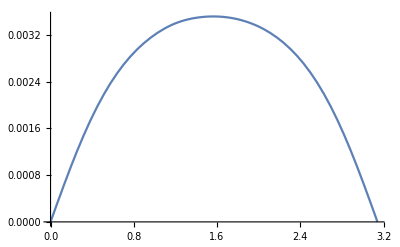

```mathematica
ClearAll[testS]
testS[chi_,chiP_]=greenScalar[eq3,100,10000,chi,chiP];//AbsoluteTiming
Plot[testS[chi,chi],{chi,0,Pi}]
```

```mathematica
testFuns[chi_,chiP_]=Table[greenScalar[eq3,1,s,chi,chiP],{s,1,5,1}]; //AbsoluteTiming
Dimensions[testFuns[x,xP]]
```

{59.2575,Null}

{5}

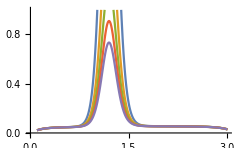

```mathematica
Plot[testFuns[chi,chi]//Evaluate,{chi,0.1,3},PlotRange->{Automatic,{0,1}}]
```

```mathematica
ClearAll[ss,s]
reconstructed={};
ellMax=20
For[ell=0,ell<ellMax,ell++,
For[ss=0,ss<101,ss=ss+10,
currentGreen[chi_,chiP_] = greenScalar[eq3,ell,ss,chi,chiP];
reconstructed=Join[reconstructed,Table[{N[chiVal,15],ell,ss,N[currentGreen[chiVal,chiVal],15]},{chiVal,chiMin,chiMax,(chiMax-chiMin)/100(* 500 *)}]];
]];//AbsoluteTiming
(* Export["greenEll100NoSineSparam.csv",reconstructed]; *)
ClearAll[ell];
Beep[]
```

{2907.01,Null}

#### Compiling Data for the determinant from TUM cluster

```mathematica
(* Results obtained from the TUM cluster *)
ellMin=81;
ellMax=100;
files = FileNames["*.csv","C:\\Users\\jscru\\LRZ Sync+Share\\dS Project\\concatenated\\greenBounce"];
files =files[[Ordering[Characters[ files]]]];
filesFV = FileNames["*.csv","C:\\Users\\jscru\\LRZ Sync+Share\\dS Project\\concatenated\\greenFV"];
filesFV =filesFV[[Ordering[Characters[ filesFV]]]];
files=Take[files,{ellMin-1,ellMax-2+1}]
filesFV= Take[filesFV,{ellMin-1,ellMax-2+1}]
(* CreateDirectory["C:\\Users\\jscru\\LRZ Sync+Share\\dS Project\\concatenated\\differenceFunctions\\"]; *)
ClearAll[dataRaw,interpData]
dataRaw = {};
For[fileIndex =1, fileIndex≤Length[files],fileIndex++,
green=Import[files[[fileIndex]]];
(*Print[StringJoin["Bounce data: ",ToString[Length[green]]]];*)
greenFV=Import[filesFV[[fileIndex]]];
(*Print[Length[greenFV]];*)
subtraction= Table[{{green[[i,1]],green[[i,2]],green[[i,3]]},green[[i,4]]-greenFV[[i,4]]},{i,1,Length[green]}];
dataRaw= Join[dataRaw , subtraction];
Print[StringJoin["Ell= ",ToString[ellMin+fileIndex-1] , " loaded and subtracted."]];
];
interpData=Interpolation[dataRaw];
Beep[]

stringSaveFile = StringJoin["C:\\Users\\jscru\\LRZ Sync+Share\\dS Project\\concatenated\\differenceFunctions\\greenSparam",ToString[ellMin],"-",ToString[ellMax],".wdx"];
Put[interpData,stringSaveFile]
Beep[]
ClearAll[dataRaw,interpData]
```

Loading Data and Computing the Determinant

```mathematica
pathToDifference ="C:\\Users\\jscru\\OneDrive - Syddansk Universitet\\2020-FalseVacuumdS\\Raw Data\\concatenated\\differenceFunctions";
dataLoad1= Get[StringJoin[pathToDifference,"\\greenSparam2-20.wdx"]];
dataLoad2 = Get[StringJoin[pathToDifference,"\\greenSparam21-40.wdx"]];
dataLoad3 = Get[StringJoin[pathToDifference,"\\greenSparam41-60.wdx"]];
dataLoad4 = Get[StringJoin[pathToDifference,"\\greenSparam61-80.wdx"]];
dataLoad5 = Get[StringJoin[pathToDifference,"\\greenSparam81-100.wdx"]];
```

```mathematica
greenFull[chi_,ell_,s_]=Piecewise[{{dataLoad1[chi,ell,s],ell≤20},{dataLoad2[chi,ell,s],20<ell≤40},{dataLoad3[chi,ell,s],40<ell≤60},{dataLoad4[chi,ell,s],60<ell≤80},{dataLoad5[chi,ell,s],80<ell}}];
```

```mathematica
dataPoints= Table[{s,greenFull[Pi/2,50,s]},{s,40000,120000,20}];
```

```mathematica
fitRules=FindFit[dataPoints,a/(b+s)^c,{a,b,c},s]
```

{a→3.7294,b→2661.21,c→1.50007}

```mathematica
fitPlot=Plot[Evaluate[a/(b+s)^c/.fitRules],{s,90000,140000},PlotStyle->{Red,Dashed,Thick}];
```

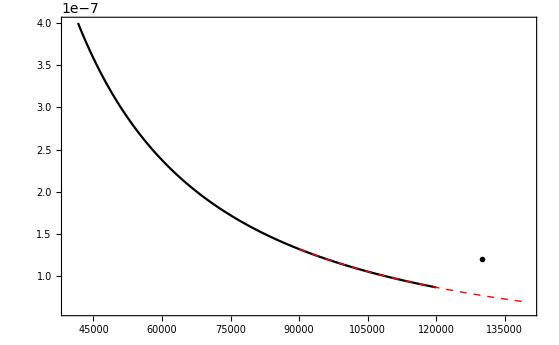

```mathematica
Show[ListLinePlot[dataPoints,PlotStyle->{Black,Line},PlotRange->{{40000,140000},{6*10^(-8),4*10^(-7)}},TicksStyle->Directive[FontFamily->"Times", 20]],fitPlot,Frame->{{True,False},{True,False}},FrameLabel->{{MaTeX["G_{b_{(50,s)}}(\\pi/2,\\pi/2)-G_{-_{(50,s)}}(\\pi/2,\\pi/2)",Magnification->1.2],None},{MaTeX["s",Magnification->1.2],None}},Epilog->Inset[Graphics[MaTeX["\\color{red}\\frac{a}{(b+s)^{1.50007}}",Magnification->1.2]],{130000,1.2*10^(-7)}]]
```

```mathematica
detPartialSum[s_]:=-(1/2)Sum[(ell+1)^2NIntegrate[greenFull[chi,ell,s],{chi,0,Pi},WorkingPrecision->10,Method->{"GlobalAdaptive","SymbolicProcessing"->0}],{ell,2,100}];
```

```mathematica
AbsoluteTiming[detPartialSum[50000]]
```

{215.626,-0.13756}

```mathematica
4*20000/500/60//N
```

2.66667

```mathematica
extraPoints=Table[{s,detPartialSum[s]},{s,110000,120000,500}];
```

```mathematica
extraPoints={{110000,-0.04479446702137290476728947180044684234`10.},{110500,-0.04449794699473714861340543065560199034`10.},{111000,-0.04420464771047337393264072839345765663`10.},{111500,-0.04391451316416048739145529612869405245`10.},{112000,-0.04362748694290880299145079165732198245`10.},{112500,-0.04334354335814469682024735986788551196`10.},{113000,-0.04306263991830284965549028678252049208`10.},{113500,-0.04278470796926440095478239267692452101`10.},{114000,-0.04250971380653169967020025890724460656`10.},{114500,-0.04223757233730196920917535456752473099`10.},{115000,-0.04196833203191199715186048262416773453`10.},{115500,-0.04170191081028555518775692695392238366`10.},{116000,-0.04143825097621318412892326977724148399`10.},{116500,-0.04117732155190659844278280184064138922`10.},{117000,-0.0409191150156640485632629071494146218`10.},{117500,-0.04066351838301850269215615204625945852`10.},{118000,-0.04041054998068768355402483556998216749`10.},{118500,-0.0401601715305623065089306682426518473`10.},{119000,-0.03991232370182666388201809857770201499`10.},{119500,-0.03966698262072136000420006006853724756`10.},{120000,-0.03942410282234050083646200607405044229`10.}}
```

{{110000,-0.04479446702},{110500,-0.04449794699},{111000,-0.04420464771},{111500,-0.04391451316},{112000,-0.04362748694},{112500,-0.04334354336},{113000,-0.04306263992},{113500,-0.04278470797},{114000,-0.04250971381},{114500,-0.04223757234},{115000,-0.04196833203},{115500,-0.04170191081},{116000,-0.04143825098},{116500,-0.04117732155},{117000,-0.04091911502},{117500,-0.04066351838},{118000,-0.04041054998},{118500,-0.04016017153},{119000,-0.0399123237},{119500,-0.03966698262},{120000,-0.03942410282}}

```mathematica
Take[extraPoints,{-5,-1}]
```

{{118000,-0.04041},{118500,-0.04016},{119000,-0.039912},{119500,-0.039666},{120000,-0.039424}}

```mathematica
model=b+a/(s)^(3/2);
```

```mathematica
fitRules=FindFit[extraPoints,model,{a,b,c,d},s,WorkingPrecision->10]
```

{a→-1.601309282×10^6,b→-0.0009056408146,c→0,d→0}

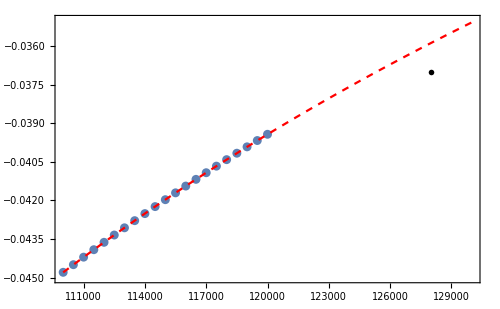

```mathematica
Show[ListPlot[extraPoints,PlotRange->{{110000,130000},{-0.045,-0.035}},Frame->{{True,False},{True,False}},FrameLabel->{{MaTeX["-\\frac{1}{2}\\sum_{\\ell=2}^{100}\\int_0^\\pi {\\rm d}\\chi\\; G_{b_{(\\ell,s)}}(\\chi,\\chi)-G_{-_{(\\ell,s)}}(\\chi,\\chi)",Magnification->1],None},{MaTeX["s",Magnification->1.4],None}}],Plot[model/.fitRules,{s,110000,130000},PlotStyle->{Red, Dashed}],Epilog->Inset[Graphics[MaTeX["\\color{red}\\frac{a}{s^{1.5}}",Magnification->1.2]],{128000,-0.037}]]
```

```mathematica
ClearAll[extrapolatedDet];
extrapolatedDet[s_] := Piecewise[{{detPartialSum[s],s<=120000},{a/(s)^c/.fitRules,s>120000}}]
```

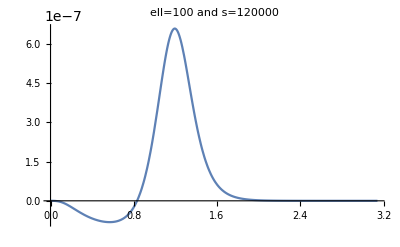

```mathematica
ellPlot = 100;
sPlot = 120000;
Plot[greenFull[chi,ellPlot,sPlot],{chi,chiMin,chiMax}, PlotRange->{Full,Full},PlotLabel->StringJoin["ell=",ToString[ellPlot]," and s=",ToString[sPlot]],AxesLabel->{MaTeX["\\chi"],MaTeX["G_b(\\chi,\\chi)-G_{\\rm fv}(\\chi,\chi)"]}]
```

```mathematica
(* Hyperspherical harmonics are already normalized with 1/2Pi^2, no need to add it *)
```

```mathematica
greenDet[ell_] := -1/2*NIntegrate[Evaluate[greenFull[chi,ell,s]],{s,0,120000},{chi,chiMin,chiMax},Method->{"GlobalAdaptive","SymbolicProcessing"->0},WorkingPrecision->6,PrecisionGoal->5]
```

```mathematica
greenDet[3]
```

-1.73842

```mathematica
(* Using the result for the WKB from the WKBJuan notebook, included a one-half which sits in front of the det in Ueff *)
```

```mathematica
greenDetMinusW0[ell_] := greenDet[ell]-1/Sqrt[ell(ell+2)]/2;
```

```mathematica
greenDetMinusW0Table = Table[{ell,greenDetMinusW0[ell]},{ell,2,100}];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

$Aborted

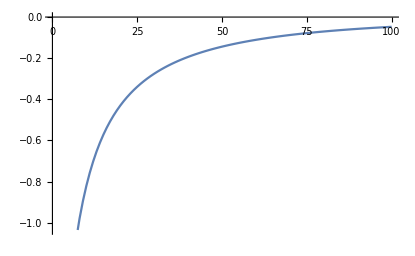

```mathematica
ListLinePlot[greenDetMinusW0Table]
```

```mathematica
Sum[greenDetMinusW0Table[[ell,2]]*(ell+1)^2,{ell,2-1,100-1}]
```

-31754.817143988206032

```mathematica
numDet =Table[{ell,greenDet[ell]*(ell+1)^2},{ell,2,100}];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

$Aborted

```mathematica
interpNumDet = Interpolation[numDet, Method->"Hermite",InterpolationOrder->1];
```

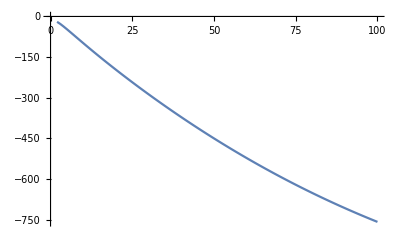

```mathematica
ListLinePlot[numDet]
```

```mathematica
Beep[]
```

```mathematica
maxEll=100;
```

```mathematica
numDetPartialSum =Table[{Lambda,Sum[numDet[[i-1,2]],{i,2,Lambda}]},{Lambda,2,maxEll}];
```

```mathematica
alphaCT = 1/2*NIntegrate[Sin[chi](m2ϕEffInterp[chi]-m2ϕEffInterp[Pi]),{chi,chiMin,chiMax},WorkingPrecision->10]
gammaCT=- 1/8*NIntegrate[Sin[chi]*(m2ϕEffInterp[chi]-m2ϕEffInterp[Pi])*((m2ϕEffInterp[chi]+m2ϕEffInterp[Pi])*Sin[chi]^2-2(Cos[chi]^2+1)),{chi,chiMin,chiMax},WorkingPrecision->10]
```

-20.45767836

330.4110772

```mathematica
ClearAll[alphaCTTable,gammaCTTable,fullCTTable];
alphaCTTable[cte_]:= Table[{Lambda,Sum[alphaCT*(ell+1)*cte,{ell,2,Lambda}]},{Lambda,2,maxEll}];
gammaCTTable[cte_] := Table[{Lambda,Sum[gammaCT/(ell+1)*cte,{ell,2,Lambda}]},{Lambda,2,maxEll}];
fullCTTable[cte_,cte2_] := Table[{Lambda,Sum[alphaCT*(ell+1)*cte+gammaCT/(ell+1)*cte2,{ell,2,Lambda}]},{Lambda,2,maxEll}];
```

```mathematica
plotRef=Plot[numDetPartialSum[[99,2]],{ell,2,100},PlotStyle->{Red}];
plotA=ListPlot[{numDetPartialSum,alphaCTTable[cte],gammaCTTable[cte2],fullCTTable[cte,cte2]}/.{cte->1/2,cte2->1/2},PlotRange->{Full,Full},PlotLegends->Automatic];
```

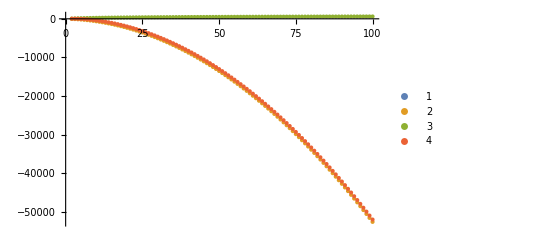

```mathematica
Show[{plotA,plotRef}]
```

```mathematica
Beep[]
```

```mathematica
(* Recheck if a Sin is needed in the measure 01.09.21 *)
```

```mathematica
ClearAll[detRaw];
detRaw[sMax_,prec_]:=-(1/2)Sum[(ell+1)^2NIntegrate[greenFull[chi,ell,s],{chi,chiMin,chiMax},{s,0,sMax},WorkingPrecision->prec,Method->{"GlobalAdaptive","SymbolicProcessing"->0}],{ell,2,100}];
```

```mathematica
detTail=NIntegrate[model-b/.fitRules,{s,120000,Infinity},WorkingPrecision->6]
```

-9245.16

```mathematica
detMax6 =detRaw[120000,6]
```

-42960.3

```mathematica
detMax7=detRaw[120000,7]
```

-42939.94

```mathematica
detMax8=detRaw[120000,8]
```

-42934.74

```mathematica
(* Highly depends on the precision still but five digits should be safe... *)
```

```mathematica
detMax5 = detRaw[120000,5]
```

-42967.

```mathematica
detMax4 = detRaw[120000,4]
```

-42950.

```mathematica
Beep[]
```

```mathematica
alphaCTSum =Sum[(ell+1)^2alphaCT/(ell+1)/2,{ell,2,100}]
```

-52658.06409

```mathematica
gammaCTSum= Sum[(ell+1)^2gammaCT/(ell+1)^3/2,{ell,2,100}]
```

610.8108873

```mathematica
detMax5+detTail-alphaCTSum-gammaCTSum
```

-160.

```mathematica
detMax4+detTail-alphaCTSum-gammaCTSum
```

-200.

```mathematica
detMax6+detTail-alphaCTSum-gammaCTSum
```

-158.

```mathematica
Beep[]
```

```mathematica
testTable =ParallelTable[{s,detRaw[s]},{s,35000,40000,250}];
```

$Aborted

```mathematica
fitParabola = LinearModelFit[testTable,{1,s,s^2},s];
fitLog = LinearModelFit[testTable,{1,Log[s]},s];
fitRational =LinearModelFit[testTable,{1,1/s,1/s^2},s];
fitLine =LinearModelFit[testTable,{1,s},s];
NSolve[Normal[fitParabola]==alphaCTSum,s]
NSolve[Normal[fitLog]==alphaCTSum,s]
NSolve[Normal[fitRational]==alphaCTSum,s]
NSolve[Normal[fitLine]==alphaCTSum,s]
```

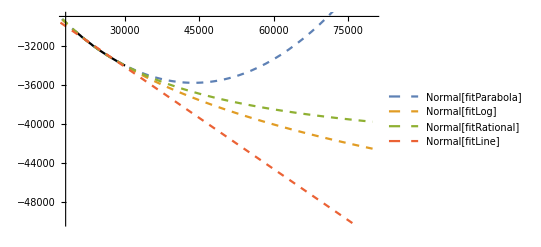

```mathematica
p1=ListLinePlot[testTable,PlotStyle->{Black},PlotRange->{{18000,80000},{-52000,-30000}}];
p2 = Plot[{Normal[fitParabola],Normal[fitLog],Normal[fitRational],Normal[fitLine]},{s,5000,80000},PlotLegends->"Expressions",PlotStyle->Dashed];
Show[p1,p2,Framed->True]
```

Computing Tadpole Functions

```mathematica
ellMax =200;
gScalarCoinPts = Import["tableGreenEll200NoSine.csv"]; 
(*gScalarHom[chi_,ell_] = 1/(-3 Cot[chi]+√(9 Cot[chi]^2+4 (s+ell (2+ell) Csc[chi]^2+Vpp[chi])))/.{Vpp[chi]->m2ϕEffInterp[chi],s->0};*)
gScalarHom[chi_,ell_] = 1/(√(4 (s+ell (2+ell) Csc[chi]^2+Vpp[chi])))/.{Vpp[chi]->m2ϕEffInterp[chi],s->0};
```

```mathematica
(* The scaling factor of the equation is extracted from the det and can be cancelled by the same factor coming from the false vacuum, the tadpole is insensitive to constants and is unaffected as verified *)
```

```mathematica
Vppp[phiP_,chi_] =D[VV,{phi,3}]//.Join[rules,{phi->phiP},{vev->1}];
(* Counterterms of the form delta0+dTad phi+dm2/2 phi^2 +deltab /3 phi^3 +ddelta/4 phi^4 *)
(* Obtained in WKB notebook *)
tadpoleCTs[phi_,chi_,Λ_]=  -1/8 beta (-2 b+6 phi) Λ^2 Sin[chi]-Λ (3/8 beta (-2 b+6 phi) Sin[chi]+3/8 beta (-2 b+6 phi) Cos[chi] Sin[chi])+Log[Λ/μ] (-17/64 beta (-2 b+6 phi) Sin[chi]-9/64 beta (-2 b+6 phi) Cos[2 chi] Sin[chi]+1/8 beta^2 (-2 b+6 phi) (-1-2 b phi+3 phi^2) Sin[chi]^3)/.Join[rules,{μ->1}];
tadpoleCTsNoCot[phi_,chi_,Λ_]=-3/8 beta (-2 b+6 phi) Λ Sin[chi]-1/8 beta (-2 b+6 phi) Λ^2 Sin[chi]+Log[Λ/μ] (-1/8 beta (-2 b+6 phi) Sin[chi]+1/8 beta^2 (-2 b+6 phi) (-1-2 b phi+3 phi^2) Sin[chi]^3)/.Join[rules,{μ->1}];
(* from the WKB solution the following exact asymptotic behavior is here for comparison *)
asympCTs[phi_,chi_,Λ_]=-115/128 beta (-2 b+6 phi) Sin[chi]-(221 beta (-2 b+6 phi) Sin[chi])/(768 Λ^2)+(51 beta (-2 b+6 phi) Sin[chi])/(128 Λ)+3/8 beta Λ (-2 b+6 phi) Sin[chi]+1/8 beta Λ^2 (-2 b+6 phi) Sin[chi]+17/64 beta EulerGamma (-2 b+6 phi) Sin[chi]-27/32 beta (-2 b+6 phi) Cos[chi] Sin[chi]+(9 beta (-2 b+6 phi) Cos[chi] Sin[chi])/(16 Λ^2)-(3 beta (-2 b+6 phi) Cos[chi] Sin[chi])/(8 Λ)+3/8 beta Λ (-2 b+6 phi) Cos[chi] Sin[chi]+1/16 beta (-2 b+6 phi) π^2 Cos[chi] Sin[chi]-27/128 beta (-2 b+6 phi) Cos[2 chi] Sin[chi]-(39 beta (-2 b+6 phi) Cos[2 chi] Sin[chi])/(256 Λ^2)+(27 beta (-2 b+6 phi) Cos[2 chi] Sin[chi])/(128 Λ)+9/64 beta EulerGamma (-2 b+6 phi) Cos[2 chi] Sin[chi]+17/64 beta (-2 b+6 phi) Log[Λ/μ] Sin[chi]+9/64 beta (-2 b+6 phi) Cos[2 chi] Log[Λ/μ] Sin[chi]+3/16 beta^2 (-2 b+6 phi) (-1-2 b phi+3 phi^2) Sin[chi]^3+(13 beta^2 (-2 b+6 phi) (-1-2 b phi+3 phi^2) Sin[chi]^3)/(96 Λ^2)-(3 beta^2 (-2 b+6 phi) (-1-2 b phi+3 phi^2) Sin[chi]^3)/(16 Λ)-1/8 beta^2 EulerGamma (-2 b+6 phi) (-1-2 b phi+3 phi^2) Sin[chi]^3+15/32 beta^2 (-2 b+6 phi) (-1-2 b phi+3 phi^2) Cos[chi] Sin[chi]^3-(9 beta^2 (-2 b+6 phi) (-1-2 b phi+3 phi^2) Cos[chi] Sin[chi]^3)/(16 Λ^2)+(3 beta^2 (-2 b+6 phi) (-1-2 b phi+3 phi^2) Cos[chi] Sin[chi]^3)/(8 Λ)-1/16 beta^2 (-2 b+6 phi) (-1-2 b phi+3 phi^2) π^2 Cos[chi] Sin[chi]^3-1/8 beta^2 (-2 b+6 phi) (-1-2 b phi+3 phi^2) Log[Λ/μ] Sin[chi]^3/.Join[rules,{μ->1}];
```

```mathematica
tableAsymp=Table[{ell,gScalarHom[Pi/2,ell]},{ell,150,200}];
model=a/ell^b;
extraFun[ell_]=model/.FindFit[tableAsymp,model,{a,b},ell]
```

0.47677261480529708121109484037480891083632/ell^0.99210005341365689608824628037330218961127

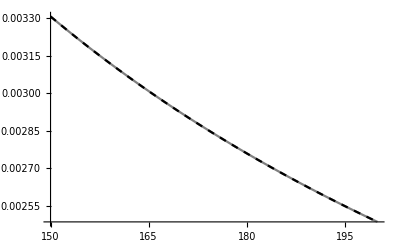

```mathematica
Plot[{scalarFun[Pi/2,ell],extraFun[ell]},{ell,150,200},PlotStyle->{Gray,{Dashed,Black}}]
```

```mathematica
ClearAll[tadpoleScalarRen]
volumeFactor= (*2Pi^2 Integrate[Sin[chi]^3,{chi,0,Pi}];*)1;
scalarFun =Interpolation[gScalarCoinPts,Method->"Hermite",InterpolationOrder->1];
tadpoleScalarBare[chi_?NumericQ,ellMax_]:=(1/2)(Vppp[bounceLoad[chi],chi])*Sum[(ell+1)^2scalarFun[chi,ell],{ell,2,ellMax}];
(*tadpoleScalarRen[chi_?NumericQ,ellMax_]:=(tadpoleScalarBare[chi,ellMax]+tadpoleCTs[bounceLoad[chi],chi,ellMax])/volumeFactor;*)
tadpoleScalarRen2[chi_?NumericQ,ellMax_]:=(tadpoleScalarBare[chi,ellMax]+tadpoleCTsNoCot[bounceLoad[chi],chi,ellMax])/volumeFactor;
```

```mathematica
tadpoleScalarHomBare[chi_?NumericQ,ellMax_]:=(1/2)(Vppp[bounceLoad[chi],chi])*Sum[(ell+1)^2Re[gScalarHom[chi,ell]],{ell,2,ellMax}];
(*tadpoleScalarHomRen[chi_?NumericQ,ellMax_]:=(tadpoleScalarHomBare[chi,ellMax]+tadpoleCTs[bounceLoad[chi],chi,ellMax])/volumeFactor;*)
tadpoleScalarHomRen2[chi_?NumericQ,ellMax_]:=(tadpoleScalarHomBare[chi,ellMax]+tadpoleCTsNoCot[bounceLoad[chi],chi,ellMax])/volumeFactor;
```

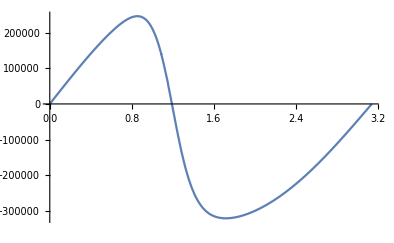

```mathematica
Plot[Re[tadpoleScalarHomBare[chi,100]],{chi,chiMin,chiMax}]
```

```mathematica
tablePts=1000;
```

```mathematica
tadpoleScalarTable = Table[{chi,tadpoleScalarBare[chi,ellMax]},{chi,chiMin,chiMax,2(chiMax-chiMin)/(tablePts)}];//Quiet
tadpoleScalarBareInterp = Interpolation[tadpoleScalarTable,Method->"Hermite",InterpolationOrder->2];
tadpoleScalarHomTable = Table[{chi,tadpoleScalarHomBare[chi,ellMax]},{chi,chiMin,chiMax,2(chiMax-chiMin)/(tablePts)}];//Quiet
tadpoleScalarHomBareInterp = Interpolation[tadpoleScalarHomTable,Method->"Hermite",InterpolationOrder->2];
(*tadpoleScalarRenTable = Table[{chi,tadpoleScalarRen[chi,ellMax]},{chi,chiMin,chiMax,2(chiMax-chiMin)/(600)}];//Quiet*)
(*tadpoleScalarRenInterp = Interpolation[tadpoleScalarRenTable,Method->"Hermite",InterpolationOrder->1];*)
tadpoleScalarRenTable2 = Table[{chi,tadpoleScalarRen2[chi,ellMax]},{chi,chiMin,chiMax,2(chiMax-chiMin)/(tablePts)}];//Quiet
tadpoleScalarRenInterp2 = Interpolation[tadpoleScalarRenTable2,Method->"Hermite",InterpolationOrder->2];
tadpoleScalarHomRenTable = Table[{chi,tadpoleScalarHomRen2[chi,ellMax]},{chi,chiMin,chiMax,2(chiMax-chiMin)/(tablePts)}];//Quiet
tadpoleScalarHomRenInterp2 = Interpolation[tadpoleScalarHomRenTable,Method->"Hermite",InterpolationOrder->2];
```

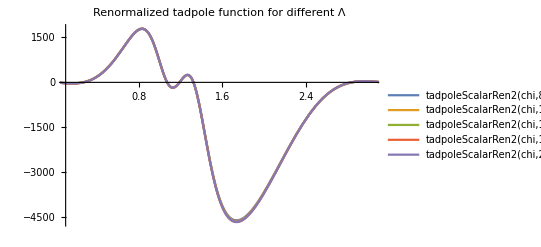

```mathematica
Plot[Evaluate@Join[Table[tadpoleScalarRen2[chi,cutOff],{cutOff,ellMax-4*30,ellMax,30}](*,Table[tadpoleScalarRen2[chi,cutOff],{cutOff,80,100,10}]*)],{chi,chiMin,chiMax},PlotLabel->"Renormalized tadpole function for different Λ",PlotLegends->"Expressions",PlotRange->{{0.1,Pi-0.1},Automatic}]//Quiet
```

```mathematica
tadpoleScalarRen[0.6,200]-tadpoleScalarRen[0.6,180]
```

-982.738

```mathematica
tadpoleScalarRen[0.6,180]-tadpoleScalarRen[0.6,160]
```

-982.983

```mathematica
tadpoleScalarRen[0.6,160]-tadpoleScalarRen[0.6,140]
```

-983.289

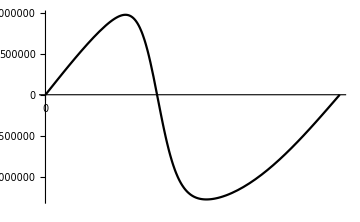
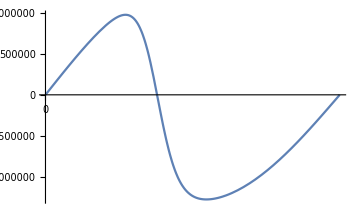
-Graphics--Graphics--Graphics- | -Graphics-

```mathematica
Grid[{{Labeled[Labeled[Plot[tadpoleScalarBareInterp[chi],{chi,chiMin,chiMax},PlotStyle->Black,Ticks->{sigmaTicks,Automatic},ImageSize->Medium],MaTeX["\\sigma \\quad\\bigg[\\frac{1}{H}\\bigg]",Magnification->1.2],Right],MaTeX["\\Pi (\\sigma)\\phi(\\sigma)",Magnification->1.2],Left,RotateLabel->True],Plot[-tadpoleCTsNoCot[bounceLoad[chi],chi,ellMax],{chi,chiMin,chiMax},Ticks->{sigmaTicks,Automatic},ImageSize->Medium]}}]
```

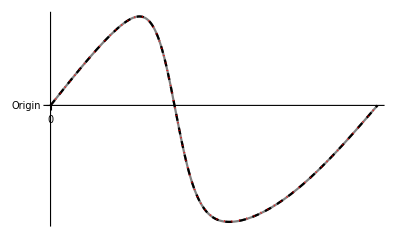
-Graphics--Graphics-

```mathematica
tadpoleTicks={{-beta ellMax^2/3/.rules,MaTeX["-\\frac{\\beta \\Lambda^2}{3}",Magnification->1]},{0,"Origin"},{beta ellMax^2/3/.rules,MaTeX["\\frac{\\beta \\Lambda^2}{3}",Magnification->1]}};
tadpoleTicks2={{-2beta^2/.rules,MaTeX["-2\\beta^2",Magnification->1]},{-beta^2/.rules,MaTeX["-\\beta^2",Magnification->1]},{0,0},{beta^2 /.rules,MaTeX["\\beta^2",Magnification->1]}};
Labeled[Plot[{Re[tadpoleScalarHomBareInterp[chi]],tadpoleScalarBareInterp[chi],-tadpoleCTsNoCot[bounceLoad[chi],chi,ellMax]},{chi,chiMin,chiMax},
PlotStyle->{{Gray,Thick},{Black,Dashed},{Red,Dotted}},Ticks->{sigmaTicks,tadpoleTicks},PlotLegends->Placed[{{MaTeX["\\Pi_{\\rm Hom}(\\sigma)",Magnification->1.2],MaTeX["\\Pi(\\sigma)",Magnification->1.2],MaTeX["-\\int {\\rm d}\\Omega_3\\frac{\\delta{\\cal L}_{\\rm ct}[\\phi]}{\\delta \\phi(\\sigma)}",Magnification->1.2],"Ren. Tadpole"}},Below]],MaTeX["\\sigma",Magnification->1.2],Right](*(*, MaTeX["\\Pi (\\sigma)\\phi(\\sigma)",Magnification->1.2]*),"",RotateLabel->True]*)
```

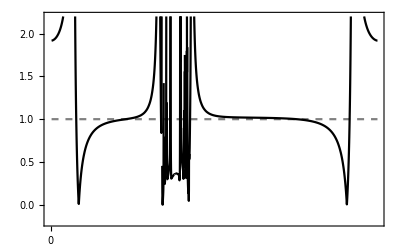
-Graphics--Graphics--Graphics-

```mathematica
Labeled[Plot[{1,Abs[tadpoleScalarRenInterp2[chi]/tadpoleScalarHomRenInterp2[chi]]},{chi,0.01,3.13},PlotRange->{Automatic,{-0.2,2.2}},PlotStyle->{{Gray,Dashed,Thin},{Line,Black}},Axes->False,Frame->True,FrameTicks->{{Automatic,Automatic},{sigmaTicks,Automatic}},WorkingPrecision->10],{MaTeX["\\sigma",Magnification->1.2],MaTeX["\\frac{\\Pi^{\\rm ren}(\\sigma)}{\\Pi_{\\rm hom}^{\\rm ren}(\\sigma)}\\vspace{3cm}",Magnification->1.2]},{Bottom,Left},RotateLabel->False]
```

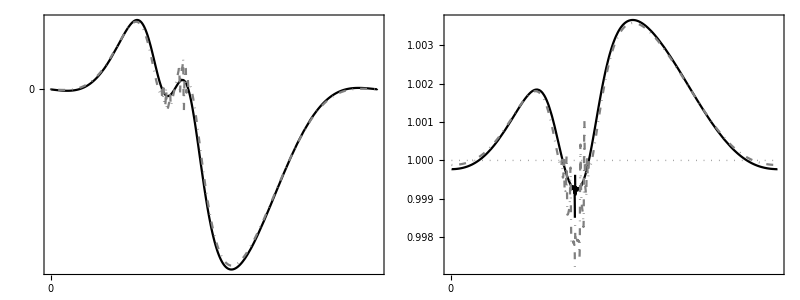

```mathematica
Grid[{{Plot[{tadpoleScalarRenInterp2[chi],tadpoleScalarHomRenInterp2[chi]},{chi,chiMin,chiMax},PlotStyle->{{Black,Line},{Gray,DotDashed}}(*PlotLabel->MaTeX[StringJoin["\\ell_{\\rm max} = ",ToString[ellMax]],Magnification->1.2]*),PlotRange->{{tol,Pi-tol},Automatic},Frame->True,FrameTicks->{{tadpoleTicks2,Automatic},{sigmaTicks,Automatic}},PlotRangePadding->Scaled[0.065],FrameLabel->{MaTeX["\\sigma",Magnification->1.2],None},ImageSize->{400}],Plot[{1,-tadpoleScalarBareInterp[chi]/tadpoleCTsNoCot[bounceLoad[chi],chi,ellMax],-tadpoleScalarHomBareInterp[chi]/tadpoleCTsNoCot[bounceLoad[chi],chi,ellMax]},{chi,0.01,3.13},PlotRange->{Automatic,Automatic},PlotStyle->{{Gray,Dotted,Thin},{Line,Black},{Gray,DotDashed}},FrameTicks->{{Automatic,None},{sigmaTicks,None}},Frame->True,PlotRangePadding->Scaled[.03],FrameLabel->{MaTeX["\\sigma",Magnification->1.2],None},ImageSize->{400}]}}]
```

#### Computing the corrections to the bounce

```mathematica
(* Files are in SDU cloud, too big for Dropbox, missing concatenation of 2-point fun. 20.12.2021 *)
dataPathOffice = FileNameJoin[{ParentDirectory[NotebookDirectory[]],"/Raw Data/twoPointGreenRaw"}];
dataPathHome = "D:\\Juan\\OneDrive - Syddansk Universitet\\2020-FalseVacuumdS\\Raw Data\\twoPointGreenRaw";
SetDirectory[dataPathHome]
```

D:\Juan\OneDrive - Syddansk Universitet\2020-FalseVacuumdS\Raw Data\twoPointGreenRaw

```mathematica
(* Already ran the concatenation, 2-point Green function can be loaded directly with get 23.12.21 *)
```

```mathematica
dataList=FileNames["new"~~__];
```

```mathematica
negMode =Flatten[ToExpression/@Import[dataList[[1]],"Table","FieldSeparators"->";"],1];
negMode=Table[{negMode[[i,1]],negMode[[i,2]],negMode[[i,4]]},{i,1,Length[negMode]}]
```

{{0.00001,0.00001,0.},{0.00001,0.006293145307,0.},250997,{3.141582654,3.135299508,0.},{3.141582654,3.141582654,0.}}
 |  |  |  |

```mathematica
ellTwoMode =Flatten[ToExpression/@Import[dataList[[3]],"Table","FieldSeparators"->";"],1];
ellTwoMode=Table[{ellTwoMode[[i,1]],ellTwoMode[[i,2]],ellTwoMode[[i,4]]},{i,1,Length[ellTwoMode]}];
```

```mathematica
ellFourMode =Flatten[ToExpression/@Import[dataList[[5]],"Table","FieldSeparators"->";"],1];
ellFourMode=Table[{ellFourMode[[i,1]],ellFourMode[[i,2]],ellFourMode[[i,4]]},{i,1,Length[ellFourMode]}];
```

```mathematica
negModeInterp = Interpolation[negMode,Method->"Hermite",InterpolationOrder->{2,2}];
ellTwoModeInterp = Interpolation[ellTwoMode,Method->"Hermite",InterpolationOrder->{2,2}];
ellFourModeInterp = Interpolation[ellFourMode,Method->"Hermite",InterpolationOrder->{2,2}];
```

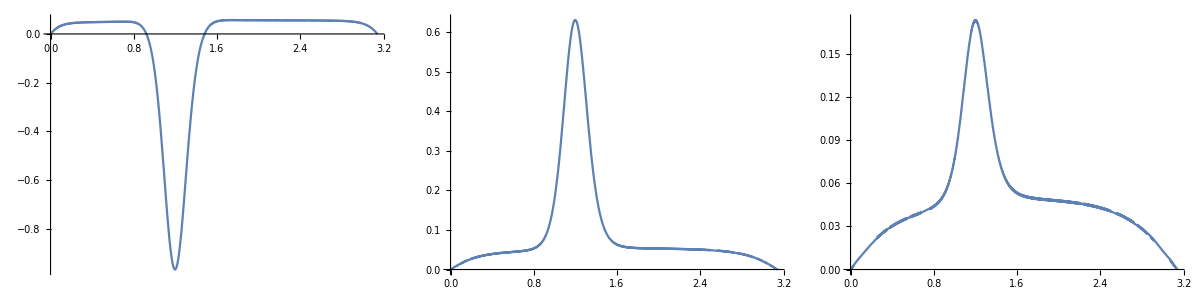

```mathematica
Grid[{{Plot[Re[negModeInterp[chi,chi]],{chi,chiMin,chiMax},PlotRange->{Automatic,Full},ImageSize->Medium],
Plot[Re[ellTwoModeInterp[chi,chi]],{chi,chiMin,chiMax},PlotRange->{Automatic,Full},ImageSize->Medium],Plot[Re[ellFourModeInterp[chi,chi]],{chi,chiMin,chiMax},PlotRange->{Automatic,Full},ImageSize->Medium]}}]
```

```mathematica
batchGreen={};
iInit=76;
iFinal=100;
For[i=iInit,i<iFinal+1,i++,
tempImport =Flatten[ToExpression/@Import[StringJoin[dataPath,Evaluate[$PathnameSeparator],dataList[[i+1]]],"Table","FieldSeparators"->";"],1];
batchGreen=Join[batchGreen,tempImport];
ClearAll[tempImport];
]
batchName=StringJoin["green2pointBatch",ToString[iInit],"-",ToString[iFinal],".dat"];
Export[batchName,batchGreen,"Table"];
Beep[]
```

green2pointBatch76-100.dat

```mathematica
dataListBatches=FileNames["green2pointBatch"~~__]
```

{green2pointBatch0-25.dat,green2pointBatch26-50.dat,green2pointBatch51-75.dat,green2pointBatch76-100.dat}

```mathematica
concatenated={};
For[item=1,item<Length[dataListBatches]+1,item++,
concatenated=Join[concatenated,Import[dataListBatches[[item]]]];
]
```

```mathematica
batchInterp= Get["interp2pointGreen.wdx"];
```

```mathematica
Manipulate[Plot3D[Log[Abs@batchInterp[chi,chiP,ellTest]],{chi,chiMin,chiMax},{chiP,chiMin,chiMax},PlotRange->{Automatic,Automatic,{-100,1}}],{ellTest,0,100}]
```

Plot3D::plln: Limiting value chiMin in {chi,chiMin,chiMax} is not a machine-sized real number.

```mathematica
(* There was no need to use the full Green's function but only the ell=0 mode 25.12.21 *)
```

```mathematica
green2ptChi=Flatten[Table[{chiVal,chiValP,Sum[batchInterp[chiVal,chiValP,ell],{ell,0,100}]},{chiVal,chiMin,chiMax,(chiMax-chiMin)/500},{chiValP,chiMin,chiMax,(chiMax-chiMin)/500}],1]
```

{{1/10000,1/10000,3.35103×10^-6},{1/10000,1/10000+1/500 (-1/5000+π),0.000232361},{1/10000,1/10000+1/250 (-1/5000+π),0.000123427},250995,{-1/10000+π,1/10000+249/250 (-1/5000+π),0.000123812},{-1/10000+π,1/10000+499/500 (-1/5000+π),0.000232426},{-1/10000+π,-1/10000+π,3.35191×10^-6}}
 |  |  |  |

```mathematica
Put[green2ptChi,"green2ptEllsummed.dat"]
```

```mathematica
green2ptChi=Get["green2ptEllsummed.dat"]
```

{{1/10000,1/10000,0.00332549},{1/10000,1/10000+1/500 (-1/5000+π),0.228855},{1/10000,1/10000+1/250 (-1/5000+π),0.000357549},250995,{-1/10000+π,1/10000+249/250 (-1/5000+π),0.000358033},{-1/10000+π,1/10000+499/500 (-1/5000+π),0.228856},{-1/10000+π,-1/10000+π,0.00332552}}
 |  |  |  |

```mathematica
Beep[]
```

```mathematica
(* green2ptChiInterp=Interpolation[batchInterp[chiVal,chiValP,0],InterpolationOrder->1] *)
```

Interpolation::innd: First argument in «405628760 bytes» does not contain a list of data and coordinates.

```mathematica
Plot3D[Log[Abs@green2ptChiInterp[chiVal,chiValP]],{chiVal,chiMin,chiMax},{chiValP,chiMin,chiMax},PlotRange->{Automatic,Automatic,Full},PlotPoints->50]
```

-Graphics3D-

```mathematica
Manipulate[Plot[batchInterp[chiP,chi,0],{chi,chiMin,chiMax},PlotRange->{Automatic,Full}],{chiP,chiMin,chiMax}]
```

```mathematica
NIntegrate[negModeInterp[Pi/2,chiP]*tadpoleScalarRenInterp[chiP],{chiP,chiMin,chiMax},WorkingPrecision->5,Method->{Automatic,"SymbolicProcessing"->0}]//AbsoluteTiming
```

{0.111974,24.965}

```mathematica
NIntegrate[negModeInterp[Pi/2,chi],{chi,chiMin,chiMax},WorkingPrecision->6,Method->{"Trapezoidal","SymbolicProcessing"->0}]//Timing
```

{0.09375,-0.034445}

```mathematica
(* Volume factor must be extracted to obtain the effective potential (not effective action) *)
```

```mathematica
volumeFactor= 2Pi^2 Integrate[Sin[chi]^3,{chi,0,Pi}];
```

```mathematica
bounceQuantumTable =Table[{chi,-NIntegrate[negModeInterp[chi,chiP]*tadpoleScalarRenInterp2[chiP],{chiP,chiMin,chiMax},WorkingPrecision->8,Method->{Automatic,"SymbolicProcessing"->0}]},{chi,chiMin,chiMax,(chiMax-chiMin)/150}];//Quiet
bounceQuantumInterp=Interpolation[bounceQuantumTable,InterpolationOrder->2,Method->"Spline"];//Quiet
```

```mathematica
bounceQuantumTable2  =Table[{chi,-NIntegrate[(negModeInterp[chi,chiP]+3ellTwoModeInterp[chi,chiP]+5ellFourModeInterp[chi,chiP])*tadpoleScalarRenInterp2[chiP],{chiP,chiMin,chiMax},WorkingPrecision->8,Method->{Automatic,"SymbolicProcessing"->0}]},{chi,chiMin,chiMax,(chiMax-chiMin)/150}];//Quiet
bounceQuantumInterp2=Interpolation[bounceQuantumTable2,InterpolationOrder->2,Method->"Spline"];//Quiet
```

$Aborted

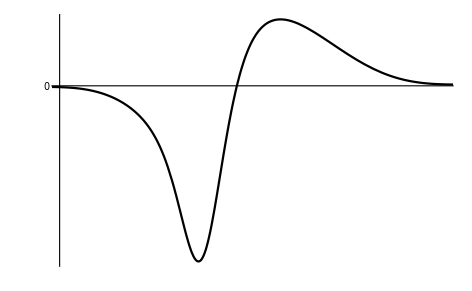

```mathematica
bounceCorrTicks={{-beta^2/16/.rules,MaTeX["-\\frac{\\beta^2}{16}",Magnification->1.2]},(*{-2beta/.rules,MaTeX["-2\\beta",Magnification->1.5]},*){-beta /.rules,MaTeX["-\\beta",Magnification->1.2]},{0,"0"},{beta /.rules,MaTeX["\\beta",Magnification->1.2]}};
Plot[{bounceQuantumInterp[chi]},{chi,chiMin,chiMax},PlotRange->{{0.1,3.05},Automatic},PlotStyle->{{Line,Black}},AxesLabel->{MaTeX["\\sigma",Magnification->1.2],None},Ticks->{sigmaTicks,bounceCorrTicks}]
Beep[]
```

```mathematica
bounceQuantumInterp[Pi/2]
```

NIntegrate::inumr: The integrand InterpolatingFunction[{{0.0001, 3.14149}}, <>][chiP] InterpolatingFunction[{<<2>>}, <>][chi, chiP] has evaluated to non-numerical values for all sampling points in the region with boundaries {{1/10000,3.141493}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

-NIntegrate[negModeInterp[chi,chiP] tadpoleScalarRenInterp2[chiP],{chiP,chiMin,chiMax},WorkingPrecision→8,Method→{Automatic,SymbolicProcessing→0}]

```mathematica
Beep[]
```

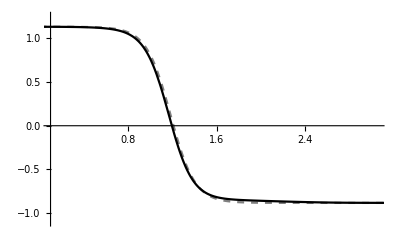

```mathematica
Plot[{bounceLoad[chi],bounceLoad[chi]+bounceQuantumInterp[chi]/beta^2/.rules},{chi,chiMin,chiMax},PlotStyle->{{Dashed,Gray},{Line,Black}},PlotRange->{{0.1,3.05},{-1.1,1.25}}]
```

```mathematica
ChebyshevU[0,x]
```

1